# Recursive Komplexity Analysis

## Importing Probability Amplitudes

### L=5 periodic

```mathematica
ACL5Psx1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sxMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psxtosy=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sxtosyPiby4.m.gz"]][[4]];
```

```mathematica
ACL5Psy1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_syMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psztosy=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sztosyPiby4.m.gz"]][[4]];
```

```mathematica
ACL5Psz1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_szMode1.m.gz"]][[4]];
```

```mathematica
ACL5Pcc1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode1.txt"]][[4]];
```

```mathematica
ACL5Pcc2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode2.txt"]][[4]];
```

```mathematica
ACL5Pcc3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode3.txt"]][[4]];
```

```mathematica
ACL5Pcc4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode4.txt"]][[4]];
```

```mathematica
ACL5Pcc5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode5.txt"]][[4]];
```

```mathematica
ACL5Psp1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_spMode1.txt"]][[4]];
```

```mathematica
ACL5Psp12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_sp12.txt"]][[4]];
```

```mathematica
ACL5Psp123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_sp123.txt"]][[4]];
```

```mathematica
ACL5Psp1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_sp1234.txt"]][[4]];
```

```mathematica
ACL5Psp12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_sp12345.txt"]][[4]];
```

```mathematica
ACL5PRNH1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_RanNormHerm1.m.gz"]][[4]];
```

```mathematica
ACL5PRNH12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_RanNormHerm12.m.gz"]][[4]];
```

```mathematica
ACL5PRNH123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_RanNormHerm123.m.gz"]][[4]];
```

```mathematica
ACL5PRNH1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_RanNormHerm1234.m.gz"]][[4]];
```

```mathematica
ACL5PRNH12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_RanNormHerm12345.m.gz"]][[4]];
```

## Getting Komplexity from the Probability Amplitudes

```mathematica
tMax=100;
tPts=500;
Prec=200;
tVals = Table[N[tMax*(i)/(tPts),Prec], {i, 1, tPts}];
```

```mathematica
cut=Length[ACL5Psx1];
PL5Psx1=Table[{tVals[[j]],Total[Abs[ACL5Psx1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx1=Table[{tVals[[j]],Range[cut].Abs[ACL5Psx1[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psxtosy];
PL5Psxtosy=Table[{tVals[[j]],Total[Abs[ACL5Psxtosy[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psxtosy=Table[{tVals[[j]],Range[cut].Abs[ACL5Psxtosy[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psy1];
PL5Psy1=Table[{tVals[[j]],Total[Abs[ACL5Psy1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy1=Table[{tVals[[j]],Range[cut].Abs[ACL5Psy1[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psztosy];
PL5Psztosy=Table[{tVals[[j]],Total[Abs[ACL5Psztosy[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psztosy=Table[{tVals[[j]],Range[cut].Abs[ACL5Psztosy[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psz1];
PL5Psz1=Table[{tVals[[j]],Total[Abs[ACL5Psz1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psz1=Table[{tVals[[j]],Range[cut].Abs[ACL5Psz1[[1;;cut,j]]]^2},{j,1,tPts}];
```

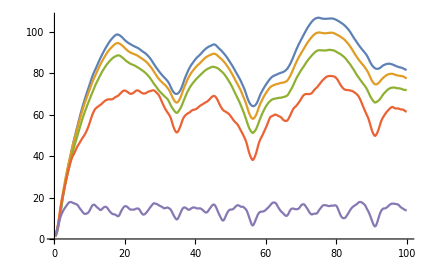

```mathematica
ListLinePlot[{KL5Psx1,KL5Psxtosy,KL5Psy1,KL5Psztosy,KL5Psz1}]
```

```mathematica
cut=Length[ACL5Pcc1];
PL5Pcc1=Table[{tVals[[j]],Total[Abs[ACL5Pcc1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc1=Table[{tVals[[j]],Range[cut].Abs[ACL5Pcc1[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc2];
PL5Pcc2=Table[{tVals[[j]],Total[Abs[ACL5Pcc2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc2=Table[{tVals[[j]],Range[cut].Abs[ACL5Pcc2[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc3];
PL5Pcc3=Table[{tVals[[j]],Total[Abs[ACL5Pcc3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc3=Table[{tVals[[j]],Range[cut].Abs[ACL5Pcc3[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc4];
PL5Pcc4=Table[{tVals[[j]],Total[Abs[ACL5Pcc4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc4=Table[{tVals[[j]],Range[cut].Abs[ACL5Pcc4[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc5];
PL5Pcc5=Table[{tVals[[j]],Total[Abs[ACL5Pcc5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc5=Table[{tVals[[j]],Range[cut].Abs[ACL5Pcc5[[1;;cut,j]]]^2},{j,1,tPts}];
```

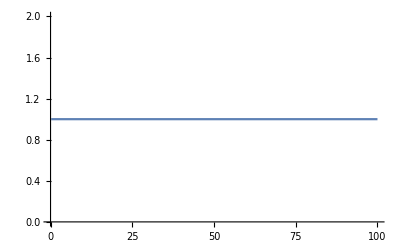

```mathematica
ListLinePlot[PL5Pcc5]
```

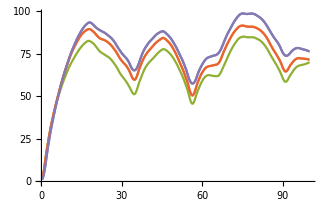

```mathematica
ListLinePlot[{KL5Pcc1,KL5Pcc2,KL5Pcc3,KL5Pcc4,KL5Pcc5}]
```

```mathematica
cut=Length[ACL5Psp1];
PL5Psp1=Table[{tVals[[j]],Total[Abs[ACL5Psp1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp1=Table[{tVals[[j]],Range[cut].Abs[ACL5Psp1[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp12];
PL5Psp12=Table[{tVals[[j]],Total[Abs[ACL5Psp12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp12=Table[{tVals[[j]],Range[cut].Abs[ACL5Psp12[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp123];
PL5Psp123=Table[{tVals[[j]],Total[Abs[ACL5Psp123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp123=Table[{tVals[[j]],Range[cut].Abs[ACL5Psp123[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp1234];
PL5Psp1234=Table[{tVals[[j]],Total[Abs[ACL5Psp1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp1234=Table[{tVals[[j]],Range[cut].Abs[ACL5Psp1234[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp12345];
PL5Psp12345=Table[{tVals[[j]],Total[Abs[ACL5Psp12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp12345=Table[{tVals[[j]],Range[cut].Abs[ACL5Psp12345[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
ListLinePlot[PL5Psp12345]
```

-Graphics-

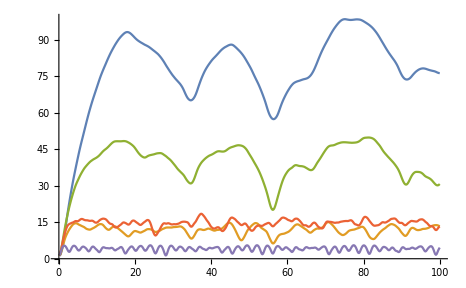

```mathematica
ListLinePlot[{KL5Psp1,KL5Psp12,KL5Psp123,KL5Psp1234,KL5Psp12345}]
```

```mathematica
cut=Length[ACL5PRNH1];
PL5PRNH1=Table[{tVals[[j]],Total[Abs[ACL5PRNH1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH1=Table[{tVals[[j]],Range[cut].Abs[ACL5PRNH1[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH12];
PL5PRNH12=Table[{tVals[[j]],Total[Abs[ACL5PRNH12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH12=Table[{tVals[[j]],Range[cut].Abs[ACL5PRNH12[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH123];
PL5PRNH123=Table[{tVals[[j]],Total[Abs[ACL5PRNH123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH123=Table[{tVals[[j]],Range[cut].Abs[ACL5PRNH123[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH1234];
PL5PRNH1234=Table[{tVals[[j]],Total[Abs[ACL5PRNH1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH1234=Table[{tVals[[j]],Range[cut].Abs[ACL5PRNH1234[[1;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH12345];
PL5PRNH12345=Table[{tVals[[j]],Total[Abs[ACL5PRNH12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH12345=Table[{tVals[[j]],Range[cut].Abs[ACL5PRNH12345[[1;;cut,j]]]^2},{j,1,tPts}];
```

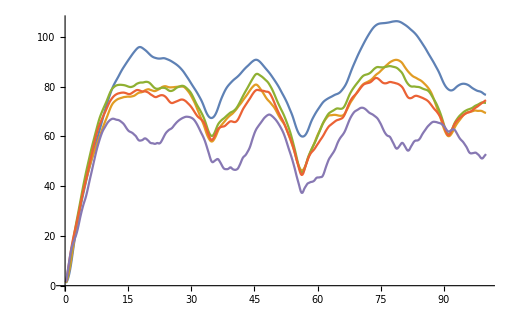

```mathematica
ListLinePlot[{KL5PRNH1,KL5PRNH12,KL5PRNH123, KL5PRNH1234, KL5PRNH12345},PlotRange->{{0,100},Automatic}]
```

## Comparisons

```mathematica
FrameSpecsKt={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->350,AspectRatio->0.67};
```

```mathematica
FrameSpecsKtMulti={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->500,AspectRatio->0.55};
```

### J-W operators as a function of sites

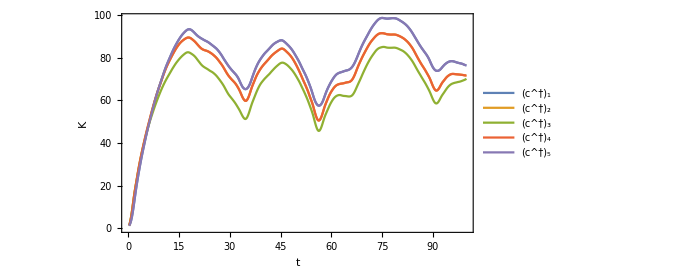

```mathematica
ListLinePlot[{KL5Pcc1,KL5Pcc2,KL5Pcc3,KL5Pcc4,KL5Pcc5},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(c^\\dagger)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(5)", TeXForm, HoldForm], Small]},{0.85,0.3}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing multi-site sigma^+ ops as function of sites

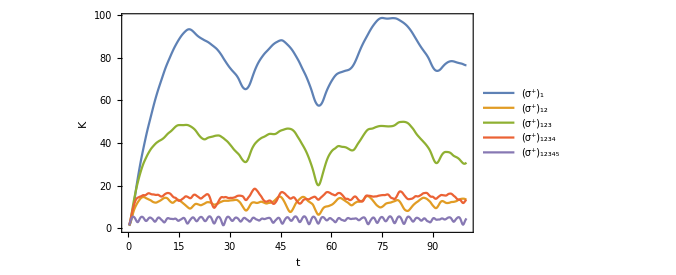

```mathematica
ListLinePlot[{KL5Psp1,KL5Psp12,KL5Psp123,KL5Psp1234, KL5Psp12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Small]},{0.1,0.75}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing multi-site random ops as a function of sites

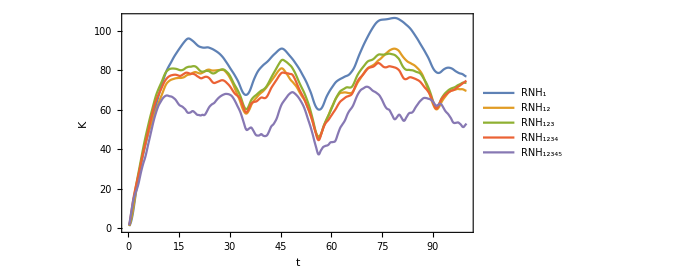

```mathematica
ListLinePlot[{KL5PRNH1,KL5PRNH12, KL5PRNH123, KL5PRNH1234, KL5PRNH12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12345)", TeXForm, HoldForm], Small]},{0.85,0.25}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Periodic Multi-site σ^+ vs J-W

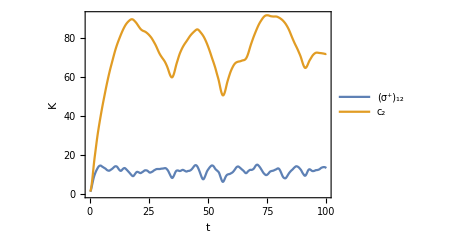

```mathematica
Psp12vsPcc2=ListLinePlot[{KL5Psp12,KL5Pcc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

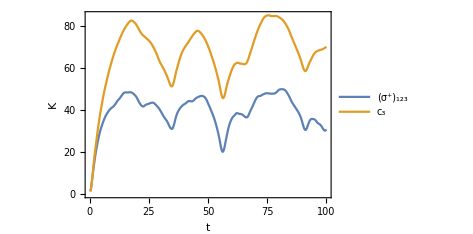

```mathematica
Psp123vsPcc3=ListLinePlot[{KL5Psp123,KL5Pcc3}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.2}],
Evaluate@Sequence@@FrameSpecsKt]
```

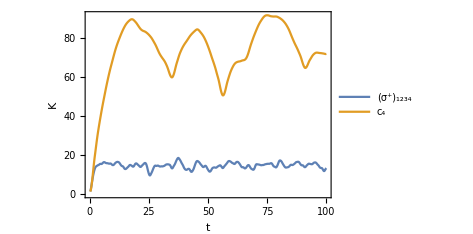

```mathematica
Psp1234vsPcc4=ListLinePlot[{KL5Psp1234,KL5Pcc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

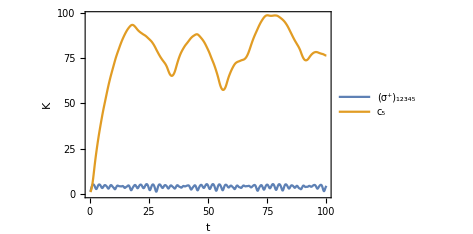

```mathematica
sp12345vscc5=ListLinePlot[{KL5Psp12345,KL5Pcc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

### Periodic Multi-site random vs J-W

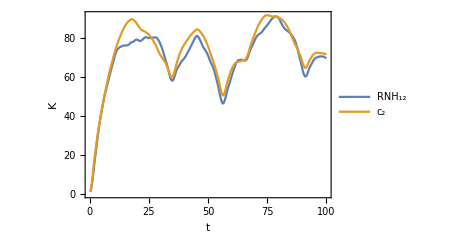

```mathematica
Psp12vsPcc2=ListLinePlot[{KL5PRNH12,KL5Pcc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

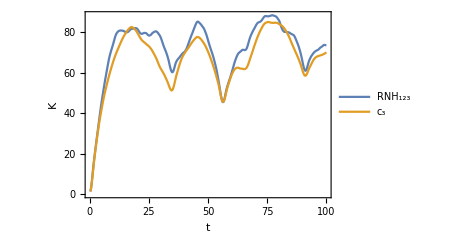

```mathematica
Psp123vsPcc3=ListLinePlot[{KL5PRNH123,KL5Pcc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

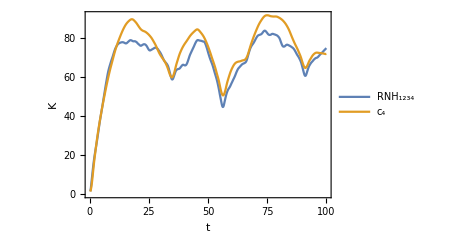

```mathematica
Psp1234vsPcc4=ListLinePlot[{KL5PRNH1234,KL5Pcc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

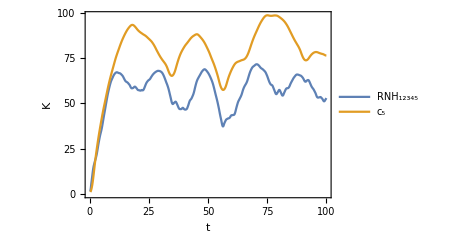

```mathematica
sp12345vscc5=ListLinePlot[{KL5PRNH12345,KL5Pcc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["\\Text{RNH}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```